```mathematica
SetDirectory["/net/home/f10/r1xu/Summer_Research/2010/AOD_Files/"];
```

```mathematica
Clear[fileName]
```

```mathematica
fileName=FileNames["*"];
```

```mathematica
size=fileName//Length
```

252

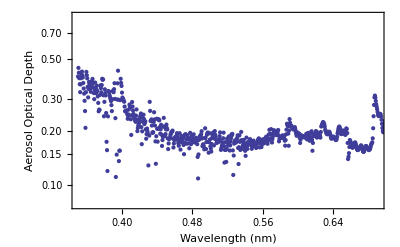

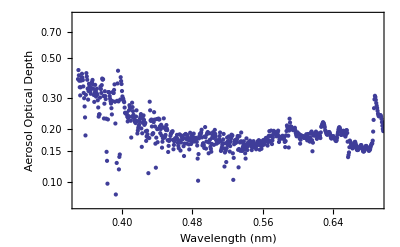

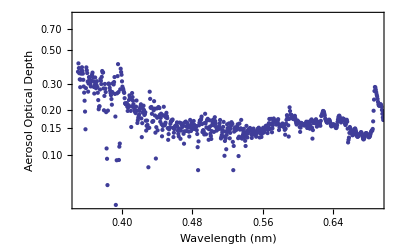

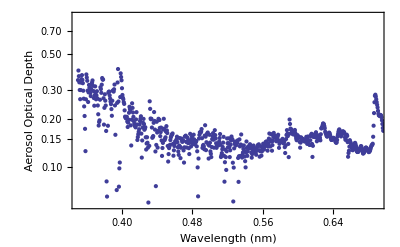

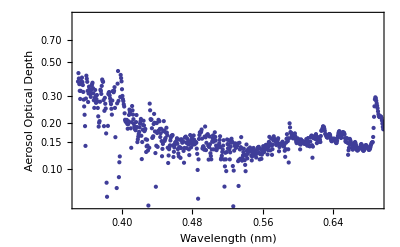

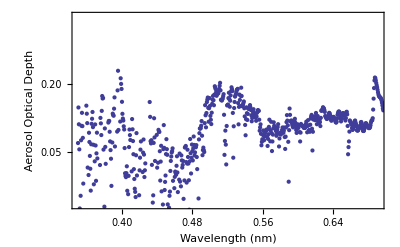

-Graphics-

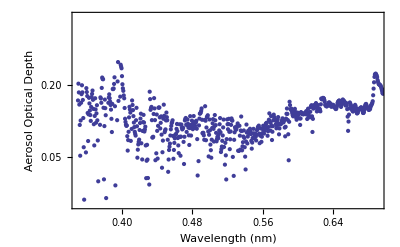

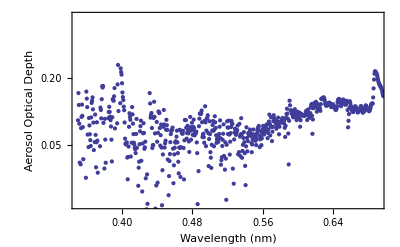

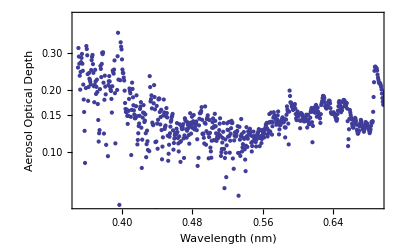

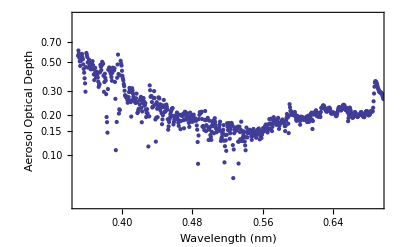

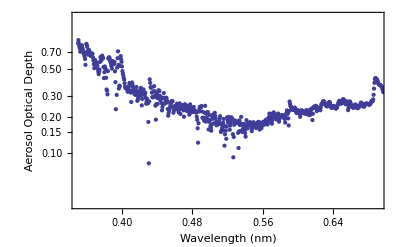

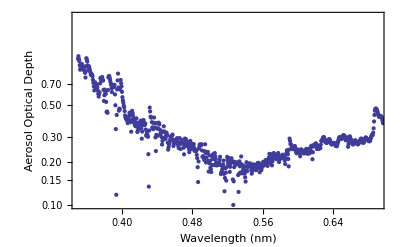

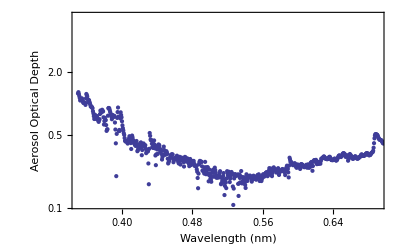

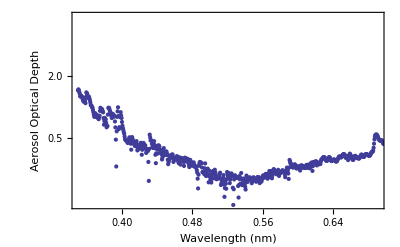

-Graphics-

-Graphics-

-Graphics-

«120 more identical outputs»

```mathematica
For[i=0, i<size, i++, data=Import[fileName[[i+1]]];
Print[ListLogPlot[data, PlotRange->{{0.35, 0.691},{0,3}}, Frame->True,FrameLabel->{"Wavelength (nm)", "Aerosol Optical Depth",fileName[[i+1]],""}]]]
```